## Stochastic population dynamics

Implements the stochastic dynamics used in Figure 4.

```mathematica
Clear["Global`*"]; 
precision=30;
$MinPrecision=precision;
SetDirectory[NotebookDirectory[]];
```

### Deterministic dynamics

```mathematica
getPositions[pop0_]:=
Block[{m0,list,extendedPop},
m0=Length[pop0];
extendedPop=Join[{0},pop0];
Table[{Total[extendedPop[[1;;i-1]]],Total[extendedPop[[1;;i]]]},{i,2,m0+1}]
];

getConcentration[n_,nutrient_]:=
Block[{i,m0,c,dc,m,cSys,cSysWrap,cSystem,dcSys,dcSysWrap,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
dc[a_,b_,α_,θ_]:=Sqrt[α/d]*(a*E^(Sqrt[α/d]*θ)-b*E^(-Sqrt[α/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];

totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[m,-z]  
];
(*returns {a1,b1,a2,b2...}: in a region σ c_i=a*E^(a*θ/d)+b*E^(-a*θ/d)+si/αi. *)

fullConcentration[n_,nutrient_]:=
Block[{a,b,c,coeff,positions,pieces,conditions,fullC},
coeff=getConcentration[n,nutrient];
positions=getPositions[n];
a=Table[coeff[[2*i-1]],{i,m}];
b=Table[coeff[[2*i]],{i,m}];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
pieces=Table[c[a[[j]],b[[j]],α[[j,nutrient]],theta-positions[[j,1]]],{j,m}];
conditions=Table[positions[[i,1]]<theta<=positions[[i,2]],{i,m}];
fullC=Piecewise[Transpose[{pieces,conditions}]]
];
```

```mathematica
getGrowth[pop_,species_,c_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,2}]//Total
];
```

```mathematica
ndot[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
n0=n0/.{x_/;x<10^-8->0};
cCoeff=Transpose[{getConcentration[n0,1],getConcentration[n0,2]}];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0
];
```

### Functions for stochasticity

```mathematica
(*project noise vector onto plane where total growth is 0*)
planeProject[u_]:=
Block[{},
normalVector=ConstantArray[1/Sqrt[Length[u]],Length[u]];
correctedVector=u-Projection[u,normalVector]
]
```

```mathematica
(*to avoid creating negative populations, we rescale the magnitude of the noise vector so that it stops at the boundary Subscript[n, σ]=0*)
rescaleNoise[n_,ν_]:=Block[{},

finalPop=n+ν;
minPop=Min[finalPop];

If[minPop<0,
mostNegativeIndex=Position[finalPop,minPop]//Flatten;
multiplier=c/.Solve[n[[mostNegativeIndex]]+c*ν[[mostNegativeIndex]]==0,c];
scaledNoise=ν*multiplier[[1]],ν]
]
```

```mathematica
noiseFn[n_]:=Block[{noise,correctedNoise,n0},
n0=n/.{x_/;x<10^-8->0};

(*Exclude extinct species*)
nonzero=Position[n,x_/;x≠0]//Flatten;

(*generate noise from Normal distribution with variance Subscript[ωn, σ]*)
noise=Sqrt[ω]*Table[Sqrt[n0[[i]]]*RandomVariate[NormalDistribution[0,1]],{i,nonzero}];

(*project random perturbation onto the plane of constant population*)
correctedNoise=planeProject[noise];

survivingNoise=ConstantArray[0,m];
For[i=1,i≤Length[nonzero],i++,
survivingNoise[[nonzero[[i]]]]=correctedNoise[[i]];
];

(*now, shorten vector to prevent negative populations*)
finalNoise=rescaleNoise[n0,survivingNoise]

];
```

### Environmental parameters

```mathematica
supply=1;  (*total nutrient supply*)
δ=supply;   (*death rate*)
e=25;             (* total enzyme budget*)
```

```mathematica
d=1.;(*diffusion coefficient*)
l=1;     (*system size*)
s={0.5,0.5}*supply;  (*nutrient supply vector, can be any length ≥2*)
p=Length[s];
```

### Species parameters: generate m random strategies

```mathematica
steps=1000;
```

```mathematica
(*seed the random number generator for reproducibility*)
seed=RandomInteger[1000]
SeedRandom[seed];
```

266

```mathematica
alphas={.3,.65,.7};
α=Table[{alphas[[i]],1-alphas[[i]]}*e,{i,Length[alphas]}];
```

```mathematica
m=Length[α];
strat=Table[α[[i,1]]/e,{i,m}];   (*maps strategies to continuum of nutrient 1, nutrient 2*)
```

### Stochastic parameters

```mathematica
(*noise strength: this sets the variance of the perturbation: <Subscript[ν, σ]>^2=Subscript[ωn, σ]*)
ω=.005;
```

```mathematica
(*perturbation period: every γ, we give the population a "kick" from a stochastic noise vector*)
γ=5;
```

### Integrate n_σ(t) and plot

```mathematica
nInit=l*ConstantArray[1/m,m]//N;
```

```mathematica
(*every γ steps, add noise vector satisfying above constraints*)
sol=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit,WhenEvent[Mod[t,γ]==0,n[t]->n[t]+noiseFn[n[t]]]},n,{t,0,steps}];
```

```mathematica
sol[sol["Domain"][[1,2]]]
```

{0.409816,0.590184,0.}

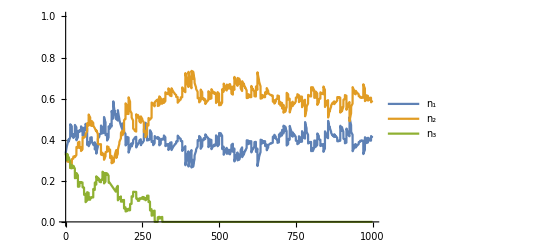

```mathematica
Plot[Evaluate[Table[Indexed[sol[t],i],{i,m}]],{t,0,steps},PlotRange->{{0,steps},{0,l}},PlotLegends->{"n_1","n_2","n_3"},TicksStyle->Directive[Black, 12],LabelStyle->Directive[Black,18]]
```

### visualize strategies

```mathematica
colors=Table[ColorData[97,i],{i,m}];
p=Table[{Graphics[{EdgeForm[{Black}],FaceForm[colors[[i]]],Disk[]}],.05},{i,m}];
```

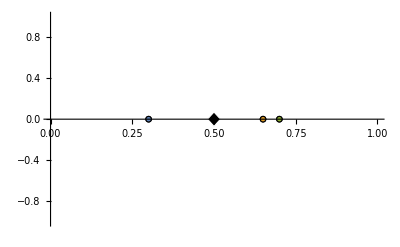

```mathematica
Show[ListPlot[Table[{{strat[[i]],0}},{i,m}],Axes->{True,False},AxesStyle->Thick,Ticks->{0,.2,.4,.6,.8,1},TicksStyle->Directive[Black, 12],PlotMarkers->p,PlotRange->{{0,1},Automatic}],Graphics[{EdgeForm[{White}],Polygon[{{s[[1]]-.02,0},{s[[1]],.07},{s[[1]]+.02,0},{s[[1]],-.07}}]}],Method->{"AxesInFront"->False}]
```

### plot trajectories on simplex in population space

#### import color schemes

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

#### Calculate deterministic steady state

```mathematica
randomInit[n_]:=RandomPoint[Simplex[l*IdentityMatrix[m]],n];
```

```mathematica
numTrials=10;
inits=randomInit[numTrials];
sols=ConstantArray[0,numTrials];
fixedPoints=ConstantArray[0,numTrials];
eigenSystems=ConstantArray[0,numTrials];
varList=Table["n"<>ToString[i]//ToExpression,{i,m}];
```

```mathematica
For[i=1,i≤numTrials,i++,
nInit=inits[[i]];
thisSol=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit},n,{t,0,10*steps}];
fixedPoints[[i]]=thisSol[10*steps];
sols[[i]]=thisSol;
];
```

#### find degenerate steady-states of corresponding well-mixed system

```mathematica
(*note that we scale supply by L to appropriately scale total population*)
```

```mathematica
wellMixedsols=Solve[{α[[1,1]]*(s[[1]]*l/(x*α[[1,1]]+y*α[[2,1]]+z*α[[3,1]]))+α[[1,2]]*(s[[2]]*l/(x*α[[1,2]]+y*α[[2,2]]+z*α[[3,2]]))==δ&&x+y+z==l},{x,y,z}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
wellMixedParametricFunction[x_]={x,y,z}/.wellMixedsols[[2]];
```

```mathematica
boundary=t/.Solve[wellMixedParametricFunction[t][[3]]==0,t];
```

#### plot well-mixed+stochastic trajectory+spatial deterministic fixed point

```mathematica
transform2Simplex[{n1_,n2_,n3_}]:=
Module[{},
{n2-n1,Sqrt[3]*n3}/l
]
```

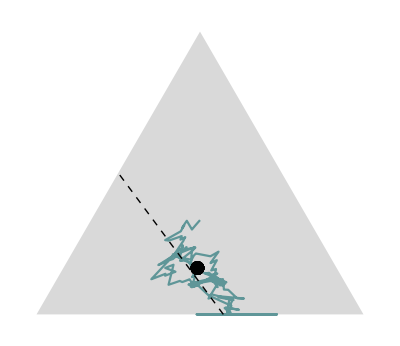

```mathematica
Show[Graphics[{LightGray,Triangle[{{-1,0},{1,0},{0,Sqrt[3]}}]}],ParametricPlot[transform2Simplex[Evaluate[Table[Indexed[sol[t],j],{j,3}]]],{t,0,steps},PlotRange->{{-1,1},{0,Sqrt[3]}},ColorFunction->Function[{x,y,t},ParulaCM[t]],ColorFunctionScaling->True],ParametricPlot[transform2Simplex[wellMixedParametricFunction[t]//Flatten],{t,10,boundary[[1]]},PlotStyle->Directive[Black,Thick,Dashed],RegionFunction->Function[{x,y},y<Sqrt[3]*(1-Abs[x])]],ListPlot[transform2Simplex/@fixedPoints,PlotStyle->Directive[Black,PointSize[.025]]]]
```

```mathematica
BarLegend[{ParulaCM,{1,steps}},ColorFunctionScaling->True,LabelStyle->Directive[Black,12],LegendLayout->"Column",Ticks->{1,500,1000}]
```